# 量子线路和量子模拟

## 癸卯年十月初七 2023年11月19日15:50:24

```mathematica
<<Wolfram`QuantumFramework`
```

## 目录

量子线路模型

单比特门

受控门

测量

通用量子门

总结

其他量子计算模型

量子模拟

## 1 量子线路模型 Quantum Circuit

本章将详细探讨量子计算，阐述量子计算的基本原理，建立量子电路的基本构造框架。
量子线路是一种描述复杂量子计算的通用语言。
目前已知的两个基础量子算法量子傅里叶变换、量子搜索算法是由这些电路在接下来两章中构造的。

## 1.1 单比特门

### X 门 和 R_X(θ)门

```mathematica
opx=QuantumOperator["X"];
opx=QuantumOperator[PauliMatrix[1]];
opx["Matrix"]//Normal//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
opx//TraditionalForm
```

01+10

```mathematica
(QuantumState/@(#/Norm[#]&/@Eigenvectors[PauliMatrix[1]]))//TraditionalForm
```

{-0/(√2)+1/(√2),0/(√2)+1/(√2)}

```mathematica
opx[QuantumState[{α,β}]]//TraditionalForm
```

β 0+α 1

```mathematica
QuantumOperator[{"RX",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[1]]//MatrixForm(*绕着x轴旋转角度θ*)
I %/.θ->Pi//MatrixForm
```

(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2])

(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2])

(0 | 1
1 | 0)

### Y 门 和 R_Y(θ)门

```mathematica
opy=QuantumOperator[PauliMatrix[2]];
opy["Matrix"]//Normal//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
QuantumOperator[{"RY",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[2]]//MatrixForm
I %/.θ->Pi//MatrixForm
```

(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2])

(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2])

(0 | -ⅈ
ⅈ | 0)

### Z 门 和 R_Z(θ)门

```mathematica
QuantumCircuitOperator["Z"];
%["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | -1)

```mathematica
QuantumOperator["Z"]//TraditionalForm
```

00-11

```mathematica
QuantumOperator[{"RZ",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[3]]//MatrixForm
I %/.θ->Pi//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(1 | 0
0 | -1)

-Graphics-

### R_n(θ) 门：绕着轴 n = (x,y,z) 旋转角度 θ

-Graphics-

```mathematica
n[i_]:={x,y,z}[[i]];
```

```mathematica
MatrixExp[-I θ/2 Sum[n[i] PauliMatrix[i],{i,3}]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify//MatrixForm
```

(Cos[θ/2]-ⅈ z Sin[θ/2] | (-ⅈ x-y) Sin[θ/2]
(-ⅈ x+y) Sin[θ/2] | Cos[θ/2]+ⅈ z Sin[θ/2])

### Hadamard 门

```mathematica
H=QuantumCircuitOperator["H"];
%["Matrix"]//Normal//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
QuantumOperator["H"]//TraditionalForm
QuantumOperator["H"]@QuantumState[{1,0}]//TraditionalForm
QuantumOperator["H"]@QuantumState[{0,1}]//TraditionalForm
```

00/(√2)+01/(√2)+10/(√2)-11/(√2)

0/(√2)+1/(√2)

0/(√2)-1/(√2)

```mathematica
(H/*H)["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
H[QuantumState[{1,0}]]//TraditionalForm
H[QuantumState[{0,1}]]//TraditionalForm
```

0/(√2)+1/(√2)

0/(√2)-1/(√2)

用 H 门制作均匀(等系数)叠加态

```mathematica
QuantumCircuitOperator["HHH"][QuantumState[{1,0,0,0,0,0,0,0}]]//TraditionalForm
```

000/(2 √2)+001/(2 √2)+010/(2 √2)+011/(2 √2)+100/(2 √2)+101/(2 √2)+110/(2 √2)+111/(2 √2)

### 相位门 S

```mathematica
QuantumOperator["S"]["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | ⅈ)

### T 门

```mathematica
QuantumOperator["T"]["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | ⅇ^((ⅈ π)/4))

### 单比特门的一般性质

#### 将一个单比特门视为对qubit的一次旋转

任何单比特门(U(2))都是旋转R_n(θ)乘一个相位

-Graphics-

u ∈ U(2),存在 s ∈ SU(2)，满足 u = e^(i α) s

```mathematica
rnt2=MatrixExp[-I θ/2 Sum[n[i] PauliMatrix[i],{i,3}]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
%//MatrixForm
```

(Cos[θ/2]-ⅈ z Sin[θ/2] | (-ⅈ x-y) Sin[θ/2]
(-ⅈ x+y) Sin[θ/2] | Cos[θ/2]+ⅈ z Sin[θ/2])

```mathematica
sol=Solve[rnt2=={{α,β},{-Conjugate[β],Conjugate[α]}},{θ,x,y,z}]//FullSimplify[#,C[1]==0&&0<θ<2π]&
```

{{x→(2 ⅈ (β-Re[β]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),y→-(2 Re[β])/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),z→(2 ⅈ (α-Re[α]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),θ→2 ArcTan[2 Re[α],√(4+α^2-Conjugate[α]^2-4 α Re[α])]},{x→-(2 ⅈ (β-Re[β]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),y→(2 Re[β])/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),z→-(2 ⅈ (α-Re[α]))/(√(4+α^2-Conjugate[α]^2-4 α Re[α])),θ→2 ArcTan[2 Re[α],-√(4+α^2-Conjugate[α]^2-4 α Re[α])]}}

2. 哈达玛门

```mathematica
h=QuantumCircuitOperator["H"]["Matrix"]//Normal;
%//MatrixForm
Det[h]
sol/.{α->√Det[h] h[[1,1]],β->√Det[h] h[[1,2]]}
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

-1

{{x→-1/(√2),y→0,z→-1/(√2),θ→π},{x→1/(√2),y→0,z→1/(√2),θ→-π}}

3. 相位门

```mathematica
s=QuantumCircuitOperator["S"]["Matrix"]//Normal;
%//MatrixForm
Det[s]
sol/.{α->√(Conjugate@Det[s])s[[1,1]],β->√(Conjugate@Det[s])s[[1,2]]}//Simplify
```

(1 | 0
0 | ⅈ)

ⅈ

{{x→0,y→0,z→1,θ→π/2},{x→0,y→0,z→-1,θ→-π/2}}

```mathematica
√Det[s] MatrixExp[-I π/4 PauliMatrix[3]]//MatrixForm//Simplify(*验证解出来的n,θ和α确实能得到S*)
```

(1 | 0
0 | ⅈ)

3维与2维的旋转的联系

-Graphics-

-Graphics-

```mathematica
Clear[n]
```

```mathematica
n[i_]:={x,y,z}[[i]];(*转轴*)
```

```mathematica
rnt2=MatrixExp[-I θ/2 Sum[n[i] PauliMatrix[i],{i,3}]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
%//MatrixForm
blc2={Cos[α/2],E^(I β)Sin[α/2]};(*变换前的qubit，α和β分别是Bloch矢量的极角与经度角*)
rp=rnt2.blc2//FullSimplify;
rp//MatrixForm
```

(Cos[θ/2]-ⅈ z Sin[θ/2] | (-ⅈ x-y) Sin[θ/2]
(-ⅈ x+y) Sin[θ/2] | Cos[θ/2]+ⅈ z Sin[θ/2])

((x-ⅈ y) Sin[α/2] (-ⅈ Cos[β]+Sin[β]) Sin[θ/2]+Cos[α/2] (Cos[θ/2]-ⅈ z Sin[θ/2])
(-ⅈ x+y) Cos[α/2] Sin[θ/2]+ⅇ^(ⅈ β) Sin[α/2] (Cos[θ/2]+ⅈ z Sin[θ/2]))

```mathematica
ρblc=KroneckerProduct[rp,ConjugateTranspose[rp]]//FullSimplify[#,(θ|α|β|z|x|y)∈Reals]&;(*变换后的态*)
```

```mathematica
blc3p=Table[Tr[ρblc.PauliMatrix[i]],{i,3}]//FullSimplify[#,{x,y,z}∈Sphere[]]&
```

{Cos[β] (1+y^2 (-1+Cos[θ])+z^2 (-1+Cos[θ])) Sin[α]-x (-1+Cos[θ]) (z Cos[α]+y Sin[α] Sin[β])+(y Cos[α]-z Sin[α] Sin[β]) Sin[θ],-Cos[α] (y z (-1+Cos[θ])+x Sin[θ])+Sin[α] ((y^2 (1-Cos[θ])+Cos[θ]) Sin[β]+Cos[β] (x y-x y Cos[θ]+z Sin[θ])),Cos[α] (z^2 (1-Cos[θ])+Cos[θ])+Sin[α] (-z (-1+Cos[θ]) (x Cos[β]+y Sin[β])+(-y Cos[β]+x Sin[β]) Sin[θ])}

```mathematica
m[1]=I D[RotationMatrix[θ,{1,0,0}],θ]/.θ->0;
m[2]=I D[RotationMatrix[θ,{0,1,0}],θ]/.θ->0;
m[3]=I D[RotationMatrix[θ,{0,0,1}],θ]/.θ->0;
```

-Graphics-

```mathematica
rnt3=MatrixExp[-I θ Sum[n[i] m[i],{i,3}]]//FullSimplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
rnt3//MatrixForm
```

(1+y^2 (-1+Cos[θ])+z^2 (-1+Cos[θ]) | x y-x y Cos[θ]-z Sin[θ] | x z-x z Cos[θ]+y Sin[θ]
x y-x y Cos[θ]+z Sin[θ] | y^2+Cos[θ]-y^2 Cos[θ] | y z-y z Cos[θ]-x Sin[θ]
x z-x z Cos[θ]-y Sin[θ] | y z-y z Cos[θ]+x Sin[θ] | z^2+Cos[θ]-z^2 Cos[θ])

```mathematica
blc3=CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,α,β}]
```

{Cos[β] Sin[α],Sin[α] Sin[β],Cos[α]}

```mathematica
blc3pp=rnt3.blc3//FullSimplify[#,{x,y,z}∈Sphere[]]&;
%//MatrixForm(*旋转后的Bloch矢量*)
```

(Cos[α] (x z-x z Cos[θ]+y Sin[θ])+Sin[α] (Cos[β] (1+y^2 (-1+Cos[θ])+z^2 (-1+Cos[θ]))-Sin[β] (x y (-1+Cos[θ])+z Sin[θ]))
(y^2 (1-Cos[θ])+Cos[θ]) Sin[α] Sin[β]-Cos[α] (y z (-1+Cos[θ])+x Sin[θ])+Cos[β] Sin[α] (x y-x y Cos[θ]+z Sin[θ])
Cos[α] (z^2 (1-Cos[θ])+Cos[θ])+Sin[α] (-z (-1+Cos[θ]) (x Cos[β]+y Sin[β])+(-y Cos[β]+x Sin[β]) Sin[θ]))

```mathematica
blc3pp-blc3p//FullSimplify[#,{x,y,z}∈Sphere[]]&//MatrixForm
```

(0
0
0)

用类似的方法可以完成下面的习题

-Graphics-

不失一般性，假设转轴沿着 z 方向

```mathematica
rnt2=MatrixExp[-I θ/2 PauliMatrix[3]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
%//MatrixForm
blc2={Cos[α/2],E^(I β)Sin[α/2]};(*变换前的qubit，α和β分别是Bloch矢量的极角与经度角*)
rp=rnt2.blc2//FullSimplify;
rp//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(ⅇ^(-(ⅈ θ)/2) Cos[α/2]
ⅇ^(1/2 ⅈ (2 β+θ)) Sin[α/2])

```mathematica
ρblc=KroneckerProduct[rp,ConjugateTranspose[rp]]//FullSimplify[#,(θ|α|β|z|x|y)∈Reals]&;(*变换后的态*)
```

```mathematica
blc3p=Table[Tr[ρblc.PauliMatrix[i]],{i,3}]//FullSimplify[#,{x,y,z}∈Sphere[]]&
```

{Cos[β+θ] Sin[α],Sin[α] Sin[β+θ],Cos[α]}

```mathematica
m[3]=I D[RotationMatrix[θ,{0,0,1}],θ]/.θ->0;
```

-Graphics-

```mathematica
rnt3=MatrixExp[-I θ  m[3]]//FullSimplify[#,{x,y,z}∈Sphere[]]&//FullSimplify;
rnt3//MatrixForm
```

(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)

```mathematica
blc3=CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,α,β}]
```

{Cos[β] Sin[α],Sin[α] Sin[β],Cos[α]}

```mathematica
blc3pp=rnt3.blc3//FullSimplify[#,{x,y,z}∈Sphere[]]&;
%//MatrixForm(*旋转后的Bloch矢量*)
```

(Cos[β+θ] Sin[α]
Sin[α] Sin[β+θ]
Cos[α])

```mathematica
blc3pp-blc3p//FullSimplify[#,{x,y,z}∈Sphere[]]&//MatrixForm
```

(0
0
0)

如何理解发生在Hilbert空间中的旋转？

量子现象发生在实验室的仪器中，与我们生活在相同的宇宙中，而不是发生在希尔伯特空间中，当粒子的z方向自旋角动量为 ℏ/2，即粒子处于|0⟩态，然后我们建立新坐标系使得新的x’轴与原来的z轴重合，那么新的量子态有确定的x方向自旋角动量，态应该变为|+⟩

描述因为旋转参考系空间的导致的态的变换，需要使用SO(3)的以单比特希尔伯特空间为表示空间的某个群表示，即SU(2)

SO(3)作用在3维线性空间上，SU(2)作用在2维希尔伯特空间上，群作用的概念使得我们能将旋转的概念从3维的实空间迁移到qubit生活的希尔伯特空间上。

演示the Belt Trick

-Graphics-

-Graphics-

#### 将单比特门视为三次旋转的复合：单比特门的 z-y-z 分解与欧拉角

-Graphics-

-Graphics-

```mathematica
QuantumOperator[{"U3",θ,β,δ}]["Matrix"]//Normal//MatrixForm
```

(Cos[θ/2] | -ⅇ^(ⅈ δ) Sin[θ/2]
ⅇ^(ⅈ β) Sin[θ/2] | ⅇ^(ⅈ (β+δ)) Cos[θ/2])

```mathematica
zyz=ⅇ^(1/2 ⅈ (β+δ)) QuantumOperator[{"RZ",β}]@QuantumOperator[{"RY",θ}]@QuantumOperator[{"RZ",δ}];
u3=zyz["Matrix"]//Normal//FullSimplify(*定理4.1*);u3//MatrixForm(*根据矩阵确定转轴和转角?*)
```

(Cos[θ/2] | -ⅇ^(ⅈ δ) Sin[θ/2]
ⅇ^(ⅈ β) Sin[θ/2] | Cos[θ/2] (Cos[β+δ]+ⅈ Sin[β+δ]))

```mathematica
Det[u3]//Simplify
```

Cos[β+δ]+ⅈ Sin[β+δ]

```mathematica
RollPitchYawMatrix[{α,β,γ},{1,2,3}]==EulerMatrix[{γ,β,α},{3,2,1}]
```

True

-Graphics-

```mathematica
(ⅇ^(1/2 ⅈ (π)) QuantumOperator[{"RZ",π/2}]@QuantumOperator[{"RX",π/2}]@QuantumOperator[{"RZ",π/2}])["Matrix"]//Normal//Simplify//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

将H分解成Ry、Rz和相位因子的积

```mathematica
ls=QuantumOperator["H"]["ZYZ"]//QuantumShortcut
QuantumOperator[%]["Matrix"]//Normal//MatrixForm
```

{{U,π/2,0,π}→{1}}

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
(ⅇ^(ⅈ (π)/2) QuantumOperator[{"RZ",0}]@QuantumOperator[{"RY",π/2}]@QuantumOperator[{"RZ",π}])["Matrix"]//Normal//Simplify//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

#### 不存在通用非门

通用非门：将任意ψ变为ψ^normal

## 1.2 多比特量子门 U(2^n)与受控操作

#### CNOT （controlled-NOT) 门

0000+0101+1011+1110

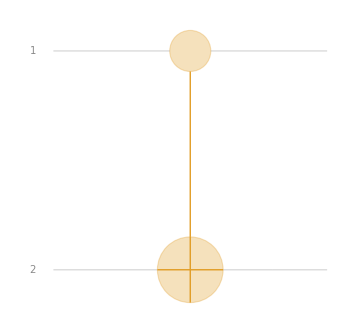

```mathematica
QuantumOperator[{"CNOT"->{1,2}}]//TraditionalForm(*模2加法*)
QuantumCircuitOperator["CNOT"]//TraditionalForm
```

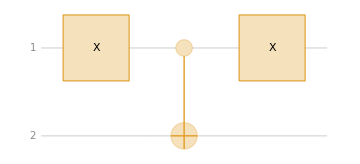

```mathematica
QuantumCircuitOperator[{"X","CNOT","X"}]//TraditionalForm
```

-Graphics-

#### 交换门

0000+0110+1001+1111

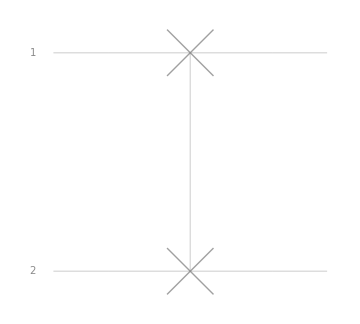

```mathematica
QuantumOperator["SWAP"]//TraditionalForm
QuantumCircuitOperator["SWAP"]//TraditionalForm
```

#### SWAP门拆成三个CNOT门

```mathematica
QuantumCircuitOperator[{"CNOT"->{1,2},"CNOT"->{2,1},"CNOT"->{1,2}}]==QuantumCircuitOperator["SWAP"]
```

True

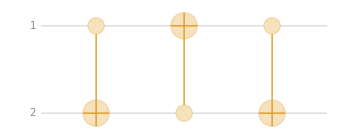

```mathematica
QuantumCircuitOperator[{QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,1}],QuantumOperator["CNOT",{1,2}]}]["Diagram"]
```

```mathematica
QuantumCircuitOperator["SWAP"]["Diagram"]
```

-Graphics-

#### Toffoli 门 和 测量

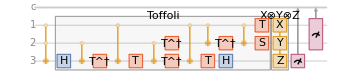

```mathematica
QuantumCircuitOperator[{QuantumOperator[…],QuantumCircuitOperator["Toffoli"],QuantumCircuitOperator[{"XYZ"}],QuantumMeasurementOperator["X",{3}],QuantumMeasurementOperator["X",{1,2}]}]["Diagram"]
```

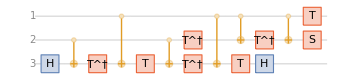

```mathematica
QuantumCircuitOperator["Toffoli"]["Diagram"]
```

```mathematica
tfl[a_,b_,c_]:={a,b,Mod[c+a b,2]}
```

```mathematica
QuantumOperator[…]["Matrix"]//Normal//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

#### CZ门

-Graphics-

```mathematica
QuantumOperator[{"Z"->{1,2}}]//TraditionalForm
QuantumOperator[{"Z"->{2,1}}]//TraditionalForm
```

0000-0101-1010+1111

0000-0101-1010+1111

#### 一般的受控U门，单比特控制单比特

-Graphics-

-Graphics-

X是泡利X矩阵

-Graphics-

-Graphics-

-Graphics-

#### 量子线路的特性

不出现回路，无环

不允许扇入扇出，扇入不可逆，扇出是量子克隆

## 1.3 测量

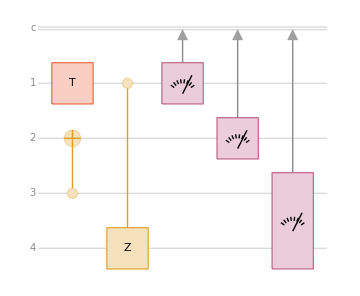

```mathematica
qc=QuantumCircuitOperator[{"T","CNOT"->{3,2},"CZ"->{1,4},{1},{2},{3,4}}];
%//TraditionalForm
```

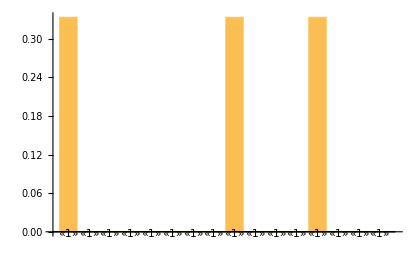

<|0000→0000,1000→ⅇ^((ⅈ π)/4) 1000,1100→ⅇ^((ⅈ π)/4) 1100|>

```mathematica
qc@QuantumState[{1,0,1,1}];
%["ProbabilityPlot"]
%%["StateAssociation"]//TraditionalForm
```

#### 延迟测量原理与经典的if-then语句

-Graphics-

-Graphics-

-Graphics-

```mathematica
inis=(QuantumCircuitOperator["HH"]@QuantumState[{1,0,0,0}])["Normalized"];
%//TraditionalForm
```

00/2+01/2+10/2+11/2

左侧

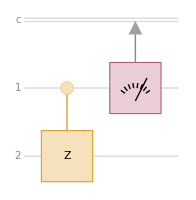

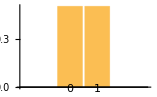

<|0→00/2+01/2,1→10/2-11/2|>

```mathematica
qc1=QuantumCircuitOperator[{"CZ",{1}}];
qc1//TraditionalForm
qmr=qc1@inis;
qmr["ProbabilityPlot"]
dst=qmr["Distribution"][[1,1]];
qmr["StateAssociation"];
%//TraditionalForm
```

```mathematica
Normal[#["Normalized"]["DensityMatrix"]]&/@qmr["StateAssociation"]//Values(*测量后的态*)
dst.%//MatrixForm
```

{{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1/2,-1/2},{0,0,-1/2,1/2}}}

(1/4 | 1/4 | 0 | 0
1/4 | 1/4 | 0 | 0
0 | 0 | 1/4 | -1/4
0 | 0 | -1/4 | 1/4)

右侧

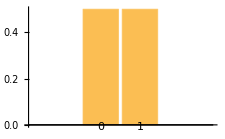

<|0→00/2+01/2,1→10/2+11/2|>

```mathematica
qmr1=QuantumMeasurementOperator[{1}]@inis;
qmr1["ProbabilityPlot"]
dst1=qmr1["Distribution"][[1,1]];
qmr1["StateAssociation"];
%//TraditionalForm
```

```mathematica
cz=QuantumOperator["CZ"]["Matrix"]//Normal
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
Normal[#["Normalized"]["DensityMatrix"]]&/@qmr1["StateAssociation"]//Values(*测量后的态*)
dst1[[1]] %[[1]]+dst1[[2]] cz.%[[2]].ConjugateTranspose[cz]//TraditionalForm
```

{{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1/2,1/2},{0,0,1/2,1/2}}}

(1/4 | 1/4 | 0 | 0
1/4 | 1/4 | 0 | 0
0 | 0 | 1/4 | -1/4
0 | 0 | -1/4 | 1/4)

#### 隐含测量原理

-Graphics-

在分析量子算法时带来一些便利。

#### Bell 基的测量

#### 测量算符 U

习题 4.34

-Graphics-

稳定子码：多比特，测量稳定子